l1

l1

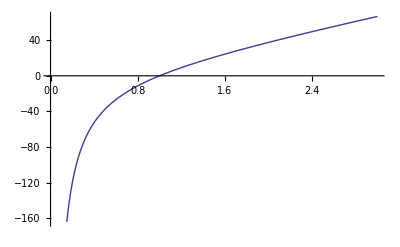

1

1

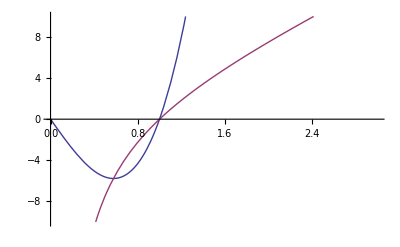

l3

(√(5-l1^2))/2

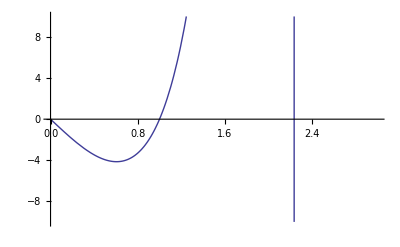

```mathematica
Clear["Global`*"]; 
(* SVK *)
l=10;m=10;
F={{l1,0,0},{0,l2,0},{0,0,l3}};
T[F_]:=1/Det[F]*(l*Tr[1/2*(Transpose[F].F-IdentityMatrix[3])]*F.Transpose[F]+m (F.Transpose[F].F.Transpose[F]-F.Transpose[F]))
l2=l1
l3=l1
Plot[T[F][[1,1]],{l1,0,3}]
l2=1
l3=1
Plot[{T[F][[1,1]],T[F][[2,2]]},{l1,0,3},PlotRange->{-10,10}]
Clear[l2,l3]
l2=l3
l3=l3/.Solve[T[F][[3,3]]==0,l3][[2]]
Plot[T[F][[1,1]],{l1,0,3},PlotRange->{-10,10}]
```